# Figures for ‘Electronically-controlled one- and two-qubit gates for transmon quasicharge qubits’

## By Nic Christopher, Updated January 9, 2025

This notebook performs the numerical analysis and generates figures 2 through 5 in the paper ‘Electronically-controlled one- and two-qubit gates for transmon quasicharge qubits’.

## Define global variables for printing

```mathematica
LPT = 72/72.27;
(*Defines conversion between LaTeX pt (traditional pica point) and the PDF standard point (desktop printing point)*)
```

## Figure 2: Band structure of (Ĥ)_T in extended Hilbert space

Creating the band structure diagram similar to Thanh Le et al. 2020.

Solve transmon system with the quasicharge degree of freedom k.

```mathematica
NUMBEROFBANDS = 2;

H[consts_][ϕ] := eC (-u''[ϕ] + 2ⅈ k u'[ϕ] + k^2 u[ϕ]) - eJ Cos[ϕ] u[ϕ] /. consts
eigenVals[consts_] := NDEigenvalues[{H[consts][ϕ],u[π]==u[-π]}, u[ϕ],{ϕ,-π,π},NUMBEROFBANDS]
band[i_] :=band[i] = Interpolation[
		Table[
{k,eigenVals[{eC-> 1.0, eJ ->1.0}][[i]]},
{k,-0.5,0.5,0.01}
]
];
```

Plot the band structure and annotate.

```mathematica
Show[Plot[Evaluate[Table[band[i][x],{i,1,NUMBEROFBANDS}]],{x,-0.5,0.5},PlotRange->{-0.6,1},PlotStyle->Thick,Frame-> True,AspectRatio->1/3,GridLines->Automatic,Axes -> False,FrameLabel->{"κ","E_b(κ)"},RotateLabel->False,ImageSize->341(*RevTex col width*),BaseStyle->{FontSize->11}],
ListPlot[{Callout[{0,band[1][0]},Style["|ψ_0⟩",RGBColor[0.368417, 0.506779, 0.709798]],{-0.1,-0.1}, CalloutMarker->"Circle", CalloutStyle -> RGBColor[0.368417, 0.506779, 0.709798]],Callout[{0.5,band[1][0.5]},Style["|ψ_1⟩",RGBColor[0.368417, 0.506779, 0.709798]],{0.4,-0.1}, CalloutMarker->"Circle", CalloutStyle -> RGBColor[0.368417, 0.506779, 0.709798]]},
PlotStyle-> None]]
```

-Graphics-

## Figure 3: Fractional Josephson effect

Creating a plot illustrating the protected level crossing of eigenstates of the effective Hamiltonian in the groundstate space for the fractional Josephson effect.

Define eigenstates of the junction fermion occupation operator, (ĝ)_0† (ĝ)_0.

```mathematica
n0[ϕ_] := 1/2 Cos[ϕ/2];
n1[ϕ_] := -1/2 Cos[ϕ/2];
```

Plot development of energies with ϕ and annotate

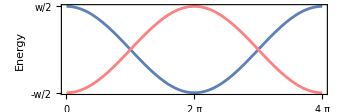

```mathematica
Show[Plot[{n0[ϕ],n1[ϕ]},{ϕ,0,4π}, FrameTicks -> {{{{0.5,"w/2"},0,{-0.5,"-w/2"}},{None}},{{0,π,2π,3π,4π},{None}}},Frame->True, FrameLabel->{"θ","Energy"},GridLines->{{π/2,π,3 π/2,2π,5 π/2,3π,7 π/2,4π},{-1/2,-1/4,0,1/4,1/2}}, PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[1, 0.5, 0.5]},ImageSize->341(*RevTex col width*),BaseStyle->{FontSize->11}],BaseStyle->{FontSize->11}, AspectRatio->1/3]
```

## Figure 4: Qubit Rabi oscillations with and without charge noise

Microscopic simulation of minimal Kitaev junction coupled to a transmon.

Define shorthand notation.

```mathematica
(*Function shorthands*)
MCommutator [A_,B_] := Commutator[A,B,{Dot,n}];
Dissipator[A_,B_] := A.B.A† - (B.A†.A + A†.A.B)/2;
FirstTwoEigensystem[A_?SquareMatrixQ] :=  Extract[1;;2]@*SortBy[First]@*Transpose@*Eigensystem @ A; 
VKroneckerProduct[vecs__?VectorQ] := Flatten@*KroneckerProduct@vecs;

(*Operator shorthands*)
{id, X, Y, Z} = PauliMatrix /@ Range[0,3];
c2 = KroneckerProduct[(X + ⅈ Y)/2, id];
c3 = KroneckerProduct[Z,(X + ⅈ Y)/2]; (*Fermion operators from Jordan-Wigner*)
SG[nMax_?(IntegerQ[#] && Positive[#]&)] := DiagonalMatrix[ ConstantArray[1,2nMax],1]; (*Susskind-Glogower operator . Remember our charge basis is doubled due to coupling of the transmon to the 4π-junction!*)
nOp[nMax_?(IntegerQ[#] && Positive[#]&)] := DiagonalMatrix[Range[-nMax,nMax]];
```

System Hamiltonian

```mathematica
hTransmon[consts_] := 16 eC (#.#&)@(nOp[nMax] - ng IdentityMatrix[2nMax+1]) - eJ/2(#.# + #† . #†)&@SG[nMax] /. consts; (*transmon Hamiltonian (Eq. 1 in paper)*)
hTunnel[consts_] :=  w(#+#†)&@KroneckerProduct[SG[nMax]†,id,c2†.c3,id]/. consts; (*tunnelling Hamiltonian*)
hTotal[consts_] := KroneckerProduct[hTransmon[consts], IdentityMatrix[16]] - Δ( KroneckerProduct[IdentityMatrix[2nMax +1],X,X,id,id] +KroneckerProduct[IdentityMatrix[2 nMax + 1],id,id,X,X]) + hTunnel[consts] /. consts; (*full system Hamiltonian (Eq. 17 in paper; here we use Δ instead of Subscript[w, F])*)

hDissip[consts_] :=(#+#†)&@KroneckerProduct[SG[nMax]†,id,c2†.c3,id]/. consts; 
(*The random perturbing Hamiltonian to impliment our noise model (this is the operator part of Eq. 26 in paper)*)
```

Shorthand for building initial states

```mathematica
densityMatrix[state_,consts_] :=densityMatrix[state,consts]= Module[{stateVectors},
(*
This function takes as input a transmon ground state (either ψ0 or ψ1) and a chain state (eg. 000+111 or eveneven+oddodd) in a human readable form. It outputs a density matrix corresponding to the state of the system with the transmon in the specified ground state and BOTH chains in the specified chain state. 
*)
stateVectors =<|
(*Some possible transmon ground states (most for these are used for testing and exploration and are not used in the final simulations in the paper)*)
"ψ0" -> KroneckerProduct[#,#†]& @FirstTwoEigensystem[hTransmon[consts]][[1,2]] ,
"ψ1" -> KroneckerProduct[#,#†]& @FirstTwoEigensystem[hTransmon[consts]][[2,2]] ,
"ψ0+ψ1" ->1/2 KroneckerProduct[#,#†]& @(FirstTwoEigensystem[hTransmon[consts]][[1,2]]+FirstTwoEigensystem[hTransmon[consts]][[2,2]]),"transmonZ" -> KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[1,2]],FirstTwoEigensystem[hTransmon[consts]][[1,2]]]- KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[2,2]],FirstTwoEigensystem[hTransmon[consts]][[2,2]]],
"transmonX" -> KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[1,2]],FirstTwoEigensystem[hTransmon[consts]][[2,2]]] + KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[2,2]],FirstTwoEigensystem[hTransmon[consts]][[1,2]]],
"transmonY"-> ⅈ (KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[2,2]],FirstTwoEigensystem[hTransmon[consts]][[1,2]]]-KroneckerProduct[FirstTwoEigensystem[hTransmon[consts]][[1,2]],FirstTwoEigensystem[hTransmon[consts]][[2,2]]]),
(*2-site chain (states shown are on BOTH chains)*)
"00+11" -> 1/4 KroneckerProduct[#,#†]& @{1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1},
"11-00" -> 1/4 KroneckerProduct[#,#†]& @{1,0,0,-1,0,0,0,0,0,0,0,0,-1,0,0,1},
"01+10" -> 1/4 KroneckerProduct[#,#†]& @{0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0},"01-10" -> 1/4 KroneckerProduct[#,#†]& @{0,0,0,0,0,1,-1,0,0,-1,1,0,0,0,0,0},
"++" -> 1/16 KroneckerProduct[#,#†]& @{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},
"eveneven+oddodd" -> 1/8 KroneckerProduct[#,#†]&@{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1},
"fullyMixed2" -> 1/16 IdentityMatrix[16],
(*3-site chain (states shown are on BOTH chains)*)
"000+111" -> 1/4 KroneckerProduct[#,#†]& @{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},
"+++" ->1/64 KroneckerProduct[#,#†]& @{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},
"011+110" ->1/4 KroneckerProduct[#,#†]& @{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
"001+100" ->1/4 KroneckerProduct[#,#†]& @{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},
"fullyMixed3" -> 1/64 IdentityMatrix[64],
"000+011+101+110" -> 1/16 KroneckerProduct[#,#†]& @{1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0},
"001+010+100+111" ->1/16 KroneckerProduct[#,#†]& @{0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1},
"101-000" -> 1/4 KroneckerProduct[#,#†]& @{1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
|>;
KroneckerProduct[stateVectors[transmon /. state],stateVectors[chains /. state]]
];
```

Compute the purity of the ‘transmon’ subsystem (recall the dofs are mixed in the new frame; see IIE of paper for details) .

```mathematica
(*Define purity of the transmon subsystem as the magnitude of its Bloch vector*)
purity[initialState_, consts_] :=Norm@{Tr[densityMatrix[{transmon->"transmonX", chains->"eveneven+oddodd"},consts].soln[initialState,consts][t]],  Tr[densityMatrix[{transmon->"transmonY", chains->"eveneven+oddodd"},consts].soln[initialState,consts][t]],Tr[densityMatrix[{transmon->"transmonZ", chains->"eveneven+oddodd"},consts].soln[initialState,consts][t]]};
```

Solve system

```mathematica
masterEquation[t_,initialStates_,consts_] := {ρ'[t]==-ⅈ MCommutator[hTotal[consts],ρ[t]] +α Dissipator[hDissip[consts]/. consts,ρ[t]],densityMatrix[initialStates,consts]==ρ[0]}/.consts;
(* The master equation for the full system dynamics (Eq. 27 in paper). We use this same equation with α = 0 to compute the unitary dynamics.*)

Clear[soln];
soln[initialStates_, consts_] := 
soln[initialStates, consts] = Module[{t},NDSolveValue[masterEquation[t,initialStates, consts],ρ,{t,0,tMax /. consts}]]
```

Plot the evolution without decoherence/ leakage due to charge noise

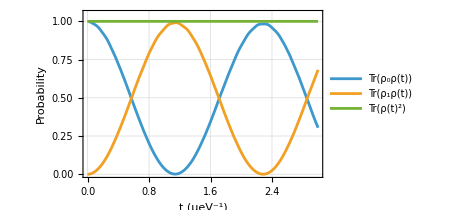

```mathematica
Block[{tFinal=3,
initialState = {transmon->"ψ0", chains->"eveneven+oddodd"},
complimentaryState = {transmon->"ψ1", chains->"eveneven+oddodd"},
consts = {nMax->3,tMax->tFinal,eC->0.01,eJ->2,ng->0,Δ->12,w->3,α->0}},
Plot[{Tr[densityMatrix[initialState,consts].soln[initialState,consts][t]],
Tr[densityMatrix[complimentaryState,consts].soln[initialState,consts][t]],
Tr[soln[initialState,consts][t].soln[initialState,consts][t]] },{t,0,tFinal},
PlotStyle->{Automatic},
PlotLegends->Placed[LineLegend[{"Tr(ρ_0ρ(t))","Tr(ρ_1ρ(t))", "Tr(ρ(t)^2)"}, LegendFunction -> (Framed[#,Background->GrayLevel[1, 0.9], FrameStyle->None]&)], {Right, Top}],
FrameLabel->{"t (μeV^-1)","Probability"},
Frame->True,
Axes->False,
PlotRange->{0,1.05},
GridLines->Automatic,
BaseStyle->{FontSize->11},
ImageSize->341(*RevTex col width*)
]
]
```

Plot the dynamics in the presence of charge noise (this is Figure 4 in paper)

```mathematica
Block[{tFinal=3,
initialState = {transmon->"ψ0", chains->"eveneven+oddodd"},complimentaryState = {transmon->"ψ1", chains->"eveneven+oddodd"},
consts = {nMax->5,tMax->tFinal,eC->0.005,eJ->1,ng->0,Δ->12,w->3}},
Plot[{Callout[Tr[densityMatrix[initialState,Append[consts,α->0]].soln[initialState,Append[consts,α->0]][t]],"Tr(ρ_0ρ(t))",{1,0.25},Scaled[0.32],FrameMargins->1, CalloutStyle-> RGBColor[0.368417, 0.506779, 0.709798], LabelStyle-> RGBColor[0.368417, 0.506779, 0.709798], CalloutMarker->"Circle"],Callout[Tr[densityMatrix[complimentaryState,Append[consts,α->0]].soln[initialState,Append[consts,α->0]][t]],"Tr(ρ_1ρ(t))",{2.25,0.2},Scaled[0.7],FrameMargins->1, CalloutStyle->  RGBColor[0.880722, 0.611041, 0.142051], LabelStyle-> RGBColor[0.880722, 0.611041, 0.142051], CalloutMarker->"Circle"],Tr[densityMatrix[initialState,Append[consts,α->0]].
soln[initialState,Append[consts,α->0.03]][t]],
Tr[densityMatrix[complimentaryState,Append[consts,α->0]].soln[initialState,Append[consts,α->0.03]][t]],Callout[purity[initialState,Append[consts,α->0.03]],"Purity",{1.74,0.87},Scaled[0.6],FrameMargins->1, CalloutStyle->RGBColor[0.560181, 0.691569, 0.194885], LabelStyle->RGBColor[0.560181, 0.691569, 0.194885],CalloutMarker->{"Circle", 17}],purity[initialState,Append[consts,α->0]]},{t,0,tFinal},
PlotStyle->{{Automatic, RGBColor[0.368417, 0.506779, 0.709798]}, {Automatic,RGBColor[0.880722, 0.611041, 0.142051]},{Dashed, RGBColor[0.368417, 0.506779, 0.709798]}, {Dashed,RGBColor[0.880722, 0.611041, 0.142051]},{Dashed,RGBColor[0.560181, 0.691569, 0.194885]},{Automatic,RGBColor[0.560181, 0.691569, 0.194885]}},
FrameLabel->{"t (ns)"},
Frame->True,
FrameTicks->{{Automatic, Automatic}, {Table[{i,0.66 i},{i,0,3,0.5}], Automatic}},
Axes->False,
PlotRange->{0,1},
GridLines->Automatic,
BaseStyle->{FontSize->11},
AspectRatio->1/2,
ImageSize->341(*RevTex col width*)
]
]
```

-Graphics-

## Figure 5: Leakage rate with Kitaev chain length using Fermi golden rule

Numerically evaluating the leakage rate formula (Eq. C11 in paper) for varying chain length and multiple parameter values.

Defining the Kitaev chain junction system in Bogoliubov-deGennes form.

```mathematica
blockX[n_] := ({{ConstantArray[0,{n,n}], IdentityMatrix[n]}, {IdentityMatrix[n], ConstantArray[0,{n,n}]}})//ArrayFlatten;
J[n_?(IntegerQ[#] && Positive[#]&)] := blockX[n].Conjugate[#]&; (* J is a charge conjugation operator on n-site Nambu spinors. J swaps spinor components and complex conjugates element-wise*)

AMatrix[n_?(IntegerQ[#] && Positive[#] && # > 1 &), consts_] := DiagonalMatrix[ConstantArray[-μ/2, n]] - t/2(DiagonalMatrix[ConstantArray[1,n-1], +1] + DiagonalMatrix[ConstantArray[1, n-1], -1]) /. consts;
BMatrix[n_?(IntegerQ[#] && Positive[#] && # > 1 &),consts_] := Δ/2(DiagonalMatrix[ConstantArray[1, n-1], +1] + DiagonalMatrix[ConstantArray[-1, n-1], -1])/. consts;
HBdG[n_?(IntegerQ[#] && Positive[#] &), consts_] := ({{AMatrix[n,consts], BMatrix[n,consts]}, {-BMatrix[n,consts], -AMatrix[n,consts]}})//ArrayFlatten;(* HBdG is the Bogoliubov-deGennes mode matrix for an n-site Kitaev chain (Eq. C12 in paper). This particular form makes use of the canonical anti-commutation relations to express HBdG in the unique form given in Eq. C12 in the paper.*)

UBdG[n_?(IntegerQ[#] && Positive[#] &), consts_] := Module[{evecs = Normalize/@Sort[Transpose[ Eigensystem[HBdG[n,consts]]]][[All,2]], matSplit, matPH} ,
(*UBdG in a unitary matrix that diagonalises HBdD (Eq. C12 in paper). *)

matSplit = Reverse[evecs[[1;;n]]];
matPH = (#~Join~(J[n]/@(#)[[1;;n]]))&@matSplit;
(*Explictly enforce particle-hole symmetry. I.e. the columns in the second half of UBdG are related to the columns of the first half by charge conjugation J. This uniquely sets the order of the columns of UBdG.*)

matPH //Transpose
]
```

Extract α, β, ψ, ϕ coefficients from U_BdG.

```mathematica
Clear[α, ψ, β, ϕ];

α[i_?(IntegerQ[#] && # >= 0 &),n_, consts_] /; i<=n :=α[ i, n, consts] = UBdG[n, consts][[n, i]];
ψ[i_?(IntegerQ[#] && # >= 0 &),n_, consts_] /; i <= n := ψ[i,n,consts] = UBdG[n,consts][[2n,i]];
(*Slice Subscript[U, BdG] to get the coefficients Subscript[α, L-1,i] and Subscript[ψ, L-1,i] required in the leakage formula (Eq. C13 in paper shows the relation between the coefficients and UBdG).*)

β[i_?(IntegerQ[#] && # >= 0 &),n_, consts_] /; i<=n :=
β[i, n, consts]=UBdG[n,consts][[1, i]];
ϕ[i_?(IntegerQ[#] && # >= 0 &),n_, consts_] /; i<=n :=
ϕ[i, n, consts]=UBdG[n,consts][[n+1, i]];
(*Slice Subscript[U, BdG] to get the coefficients Subscript[β, 0,i] and Subscript[ϕ, 0,i] required in the leakage formula (Eq. C14 in paper shows the relation between the coefficients and UBdG).*)
```

Use the transmon system and SG operator shorthand defined in the ‘Rabi Oscillations’ section to numerically evaluate the ⅇ^(±iϕ/2) matrix elements (appearing in Eq. C11 of the paper).

```mathematica
expiϕon2Element[bra_?(IntegerQ[#]&& Positive[#]&),ket_?(IntegerQ[#]&& Positive[#]&),consts_] := Sort[Transpose[Eigensystem[hTransmon[consts]]]][[bra,2]]†. SG[nMax].Sort[Transpose[Eigensystem[hTransmon[consts]]]][[ket,2]] /. consts;
 expMinusiϕon2Element[bra_?(IntegerQ[#]&& Positive[#]&),ket_?(IntegerQ[#]&& Positive[#]&),consts_] := Sort[Transpose[Eigensystem[hTransmon[consts]]]][[bra,2]]†. SG[nMax]†. Sort[Transpose[Eigensystem[hTransmon[consts]]]][[ket,2]] /.consts;
```

Write leakage formula in terms of above coefficients.

```mathematica
leakage[n_, consts_] := A ( Sum[Sum[Abs[expiϕon2Element[1,f,consts] α[i,n,consts]ϕ[j,n,consts] - expMinusiϕon2Element[1,f,consts]β[j,n,consts]ψ[i,n,consts]]^2,{i, 2, n},{j, 2, n}] + 1/2(Sum[Abs[expiϕon2Element[1,f,consts](ϕ[1,n,consts]+β[1,n,consts])α[i,n,consts]-expMinusiϕon2Element[1,f,consts](ϕ[1,n,consts]+β[1,n,consts])ψ[i,n,consts]]^2,{i, 2, n}] + Sum[Abs[expiϕon2Element[1,f,consts](ψ[1,n,consts]-α[1,n,consts])ϕ[j,n,consts]+expMinusiϕon2Element[1,f,consts](ψ[1,n,consts]-α[1,n,consts])β[j,n,consts]]^2,{j, 2, n}]),{f,1,nMax /.consts}] + 1/4 Sum[Abs[(ψ[1,n,consts] - α[1,n,consts])(ϕ[1,n,consts] + β[1,n,consts]) expiϕon2Element[1,f,consts] + (ψ[1,n,consts] - α[1,n,consts])(ϕ[1,n,consts] + β[1,n,consts]expMinusiϕon2Element[1,f,consts] )]^2,{f,3,nMax /. consts}])/.consts;
(*This is the leakage formula from Eq. C11 in the paper.*)
```

Plot leakage with chain lengths for several parameter settings and annotate.

```mathematica
Block[{maxLength = 10,
consts = {eC->0.01, eJ->2, ng->0, nMax->5, μ->j ,t->(12+j),Δ->12 +j, A->0.03}},
ListPlot[Table[Table[{l,leakage[l,consts]},{l,4,maxLength}],{j,0.,4.,2}], 
PlotRange->{{4,All},{0.0064,All}}, AspectRatio->1/2,
FrameLabel->{"L","Γ_0(L)/ℏ (μeV)"},
 Frame->True,
PlotLabels->Placed[{Style["Sweet spot",RGBColor[0.368417, 0.506779, 0.709798]],Style["μ=2μeV, w_F=14μeV",RGBColor[0.880722, 0.611041, 0.142051]],Style["μ=4μeV, w_F=16μeV",RGBColor[0.560181, 0.691569, 0.194885]]},
{{Scaled[0.38],Above},{Scaled[0.75],Below},{Scaled[0.75],Below}}],
 Joined->True,
 PlotMarkers->Automatic,
 BaseStyle->{FontSize->11},
 ImageSize->341(*RevTex col width*),
 GridLines->Automatic]]
```

-Graphics-

```mathematica
CloudPublish[EvaluationNotebook[]]
```

CloudObject[https://www.wolframcloud.com/obj/776e62d6-2632-48a0-9a1a-aef19c695d39]